## Lapse function plots f(r)

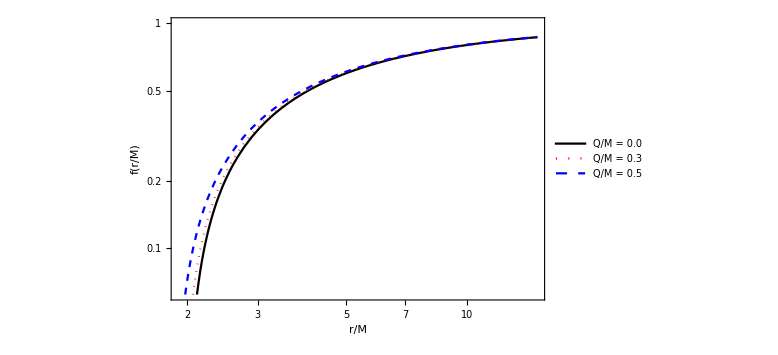

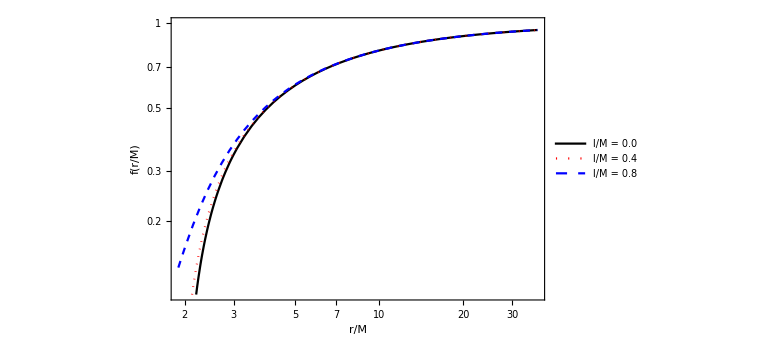

```mathematica
f[R_,Q_,l_] = 1 - ((2R-Q^2)R^2)/(R^4+(2R+Q^2)l^2);
LogLogPlot[{f[R,0.0,0.2],f[R,0.3,0.2],f[R,0.5,0.2]},{R,1.9,15},PlotLegends->Placed[{"Q/M = 0.0","Q/M = 0.3","Q/M = 0.5"},{Scaled[{0.05,0.83}],{0,0.5}}],PlotStyle->{{Black},{Dotted,Red},{Dashed,Blue}},Frame->True,FrameLabel->{"r/M","f(r/M)","l/M=0.2"},Epilog->Inset[Plot[{f[R,0.0,0.2],f[R,0.3,0.2],f[R,0.5,0.2]},{R,11.9,12.5},PlotStyle->{{Black},{Dotted,Red},{Dashed,Blue}},ImageSize->390/1.5,Frame->True],{2.,-2}],Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Large]


LogLogPlot[{f[R,0.3,0.0],f[R,0.3,0.4],f[R,0.3,0.8]},{R,1.9,37},PlotLegends->Placed[{"l/M = 0.0","l/M = 0.4","l/M = 0.8"},{Scaled[{0.05,0.83}],{0.,0.5}}],PlotStyle->{{Black},{Dotted,Red},{Dashed,Blue}},Frame->True,FrameLabel->{"r/M","f(r/M)","Q/M=0.3"},Epilog->{Inset[Plot[{f[R,0.3,0.0],f[R,0.3,0.4],f[R,0.3,0.8]},{R,11.9,12.},PlotStyle->{{Black},{Dotted,Red},{Dashed,Blue}},ImageSize->420/1.8,Frame->True],{2.7,-1.52}]},Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Large]
```

## Black hole and No black hole region

```mathematica
f[r_,Q_,l_]:= 1 - ((2*r-Q^2)*r^2)/(r^4+(2*r+Q^2)l^2);
ll=Table[l,{l,0.01,0.77,0.001}];
```

```mathematica
QQ=Table[Q/.FindRoot[{(f[r,Q,l]/.{l->ll[[i]]})==0,D[(f[r,Q,l]/.{l->ll[[i]]}),r]==0},{{r,1},{Q,1}}],{i,1,Length[ll]}];
QQll=Table[{QQ[[i]],ll[[i]]},{i,1,Length[ll]}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

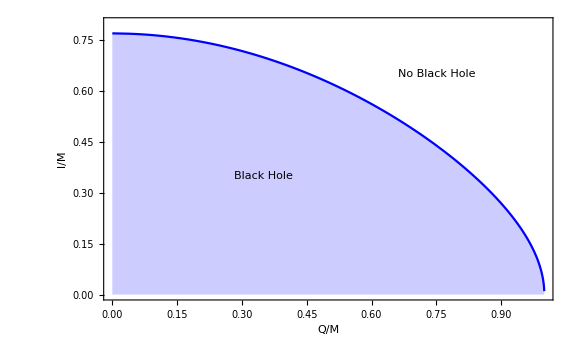

```mathematica
ListLinePlot[QQll,Frame->True,FrameLabel->{"Q/M","l/M"},Filling->Axis,LabelStyle->Directive[FontFamily->"Times",FontSize->14,FontColor->Black],PlotStyle->Blue,PlotRange->{{0.,1},{0,0.8}},BaseStyle->{14,FontFamily->"TimesNewRoman"},
Epilog->{Text[Rotate[Framed["Black Hole",FrameStyle->None,Background->None],0Degree],{0.35,0.35}],Text[Rotate[Framed["No Black Hole",FrameStyle->None,Background->None],0Degree],{0.75,0.65}]},ImageSize->Large]
```

```mathematica
l/.FindRoot[{(f[r,Q,l]/.{Q->0.3})==0,D[(f[r,Q,l]/.{Q-> 0.3}),r]==0},{{r,1},{l,1}}]
```

0.717949

```mathematica
BaseStyle->{14,FontFamily->"TimesNewRoman"},
Epilog->{Text[Rotate[Framed["Black Hole",FrameStyle->None,Background->None],0Degree],{0.25,0.25}],Text[Rotate[Framed["No Black Hole",FrameStyle->None,Background->None],0Degree],{0.75,0.55}]}
```

## The radial dependance of Effective Potentials of photons around of charged Hayward BH

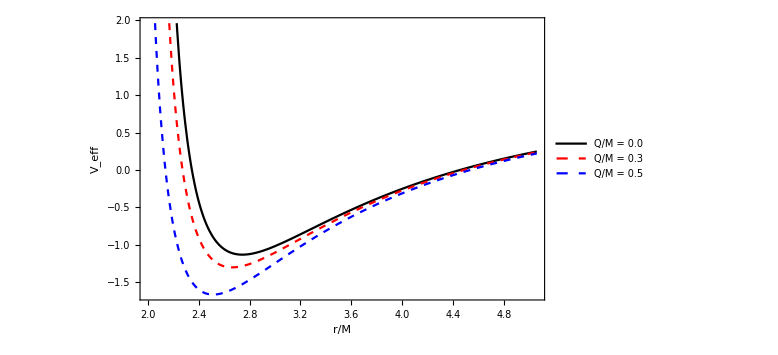

```mathematica
Vef[r_, Q_,l_,M_,Ene_,L_] := -Ene^2(-1+((2M r-Q^2)r^2)/(r^4 +(2M r+Q^2)l^2))^-1- L^2/r^2;

Plot[{Vef[r,0.0,0.2,1,1,6],Vef[r,0.3,0.2,1,1,6],Vef[r,0.5,0.2,1,1,6]},{r,2,5.06},PlotLegends->Placed[{"Q/M = 0.0","Q/M = 0.3","Q/M = 0.5"},{Scaled[{0.2,0.73}],{-1.9,2.5}}],PlotStyle->{{Black},{Dashed,Red},{Dashed,Blue}},Frame->True,FrameLabel->{"r/M","V_eff","l/M=0.2,  E/M=1,  L/M=6"},Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Large]
```

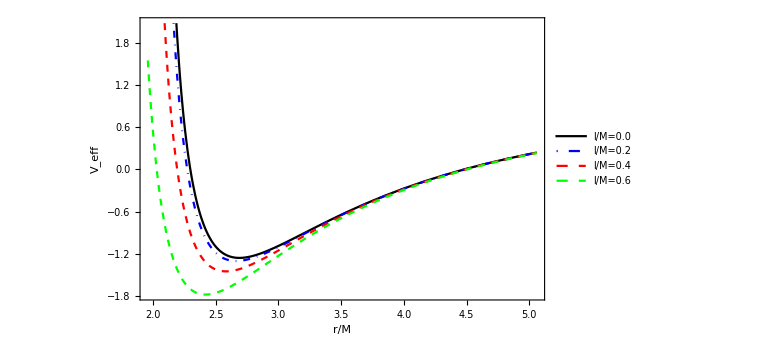

```mathematica
(*Next graph is for Veff of l which is curvature parameter Vef[r_, Q_,l_,M_,Ene_,L_] *)
Plot[{Vef[r,0.3,0.0,1,1,6],Vef[r,0.3,0.2,1,1,6],Vef[r,0.3,0.4,1,1,6],Vef[r,0.3,0.6,1,1,6]},{r,1.959,5.06},PlotStyle->{{Black},{DotDashed,Blue}, {Dashed,Red}, {Dashed,Green},{Dashed,Green}}, FrameLabel->{"r/M","V_eff","Q/M=0.3,E/M=1,L/M=6"},Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},PlotLegends->Placed[{"l/M=0.0","l/M=0.2","l/M=0.4","l/M=0.6","l/M=0.8"},{Scaled[{0.8,0.56}],{0.2,1.47}}],ImageSize->Large]
```

## Photon sphere radius as a function of the space-time parameters Q(charge of BH) and l (legth parameter -> g^3= 2 Ml^2 )

```mathematica
(*Photon Sphere some cases*)
Solve[Vef[r, Q,l,M,Ene,L]==0,Ene]//Simplify
```

{{Ene→-(L √((l^2 (Q^2+2 r)+r^2 (Q^2+(-2+r) r))/(r^4+l^2 (Q^2+2 r))))/r},{Ene→(L √((l^2 (Q^2+2 r)+r^2 (Q^2+(-2+r) r))/(r^4+l^2 (Q^2+2 r))))/r}}

```mathematica
D[Vef[r, Q,l,M,Ene,L],r]/.Ene->-(L √((l^2 (Q^2+2 M r)+r^2 (Q^2+r (-2 M+r)))/(r^4+l^2 (Q^2+2 M r))))/r//Simplify
```

Vef^(1,0,0,0,0,0)[r,Q,l,M,-(L √((l^2 (Q^2+2 M r)+r^2 (Q^2+r (-2 M+r)))/(r^4+l^2 (Q^2+2 M r))))/r,L]

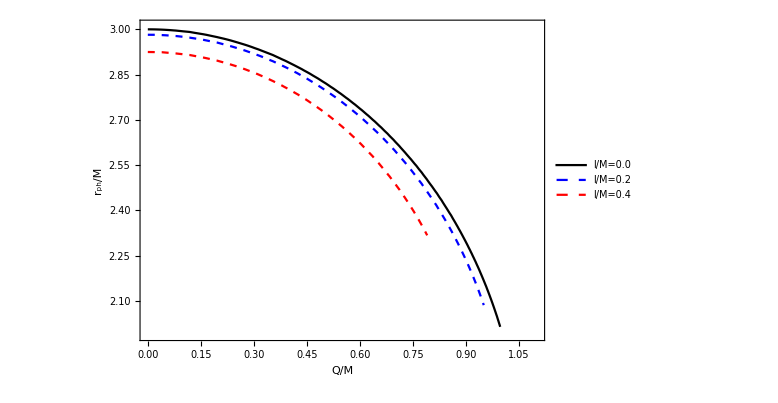

```mathematica
(2 L^2 (l^4 (Q^2+2 M r)^2+r^6 (2 Q^2+r (-3 M+r))+2 l^2 r^3 (Q^2 r+M (Q^2+2 r^2))))/(r^3 (r^4+l^2 (Q^2+2 M r)) (l^2 (Q^2+2 M r)+r^2 (Q^2+r (-2 M+r))));
M=1;
l1 = 0.0;
l3 = 0.2;
l5 = 0.4;

FR[Q_,r_]=If[Q≤0.79,(l5^4 (Q^2+2 M r)^2+r^6 (2 Q^2+r (-3 M+r))+2 l5^2 r^3 (Q^2 r+M (Q^2+2 r^2)))/(r^3 (r^4+l5^2 (Q^2+2 M r)) (l5^2 (Q^2+2 M r)+r^2 (Q^2+r (-2 M+r)))),None];
FB[Q_,r_]=If[Q≤.95,(l3^4 (Q^2+2 M r)^2+r^6 (2 Q^2+r (-3 M+r))+2 l3^2 r^3 (Q^2 r+M (Q^2+2 r^2)))/(r^3 (r^4+l3^2 (Q^2+2 M r)) (l3^2 (Q^2+2 M r)+r^2 (Q^2+r (-2 M+r)))),None];
Fb[Q_,r_]=If[Q≤1.001,(l1^4 (Q^2+2 M r)^2+r^6 (2 Q^2+r (-3 M+r))+2 l1^2 r^3 (Q^2 r+M (Q^2+2 r^2)))/(r^3 (r^4+l1^2 (Q^2+2 M r)) (l1^2 (Q^2+2 M r)+r^2 (Q^2+r (-2 M+r)))),None];
ContourPlot[{Fb[Q,r]==0, FB[Q,r]==0,FR[Q,r]==0},{Q,0,1.1},{r,1.989,3.01},PlotLegends->Placed[{"l/M=0.0","l/M=0.2","l/M=0.4"},{Scaled[{0.715,0.86}],{0,0.5}}],ContourStyle->{{Black},{Dashed,Blue},{Dashed,Red},{Dashed,Yellow},{Dashed,Green}},FrameLabel->{" Q/M","r_ph/M"},AspectRatio->0.7,Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Large]
```

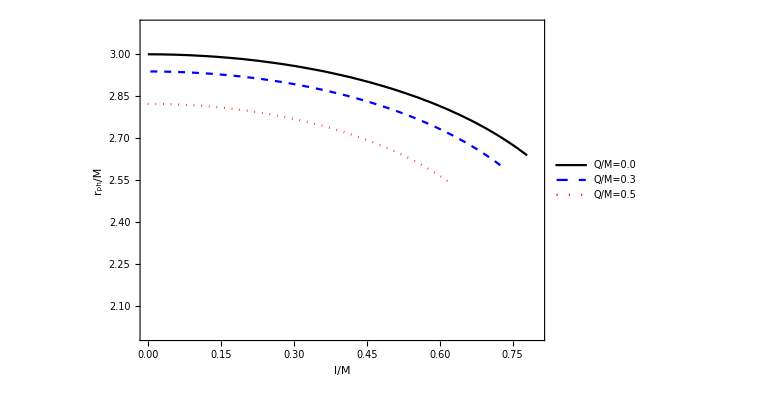

```mathematica
(*rphs of l - curv.parameter*)

Q1 = 0.0;
Q2 = 0.3;
Q3 =0.5;

rB[l_,r_] = If[l≤0.79,(l^4 (Q1^2+2 r)^2+r^6 (2 Q1^2+(-3+r) r)+2 l^2 r^3 (Q1^2+Q1^2 r+2 r^2))/(r^3 (r^4+l^2 (Q1^2+2 r)) (l^2 (Q1^2+2 r)+r^2 (Q1^2+(-2+r) r))),None];
rb[l_,r_] = If[l≤.725,(l^4 (Q2^2+2 r)^2+r^6 (2 Q2^2+(-3+r) r)+2 l^2 r^3 (Q2^2+Q2^2 r+2 r^2))/(r^3 (r^4+l^2 (Q2^2+2 r)) (l^2 (Q2^2+2 r)+r^2 (Q2^2+(-2+r) r))),None];
rR[l_,r_] = If[l≤.623,(l^4 (Q3^2+2 r)^2+r^6 (2 Q3^2+(-3+r) r)+2 l^2 r^3 (Q3^2+Q3^2 r+2 r^2))/(r^3 (r^4+l^2 (Q3^2+2 r)) (l^2 (Q3^2+2 r)+r^2 (Q3^2+(-2+r) r))),None];
ContourPlot[{rB[l,r]==0,rb[l,r]==0, rR[l,r]==0},{l,0.0,0.78},{r,2.5,3.13},PlotLegends->Placed[{"Q/M=0.0","Q/M=0.3","Q/M=0.5"},{Scaled[{0.10,0.55}],{0,0.5}}],FrameLabel->{"l/M","r_ph/M"},ContourStyle->{{Black},{Dashed,Blue},{Dotted,Red}},AspectRatio->0.7,Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Large,PlotRange->{{0,0.8},{2,3.1}}]
```

## Event Horizon sphere radius as a function of space-time parameters Q and l

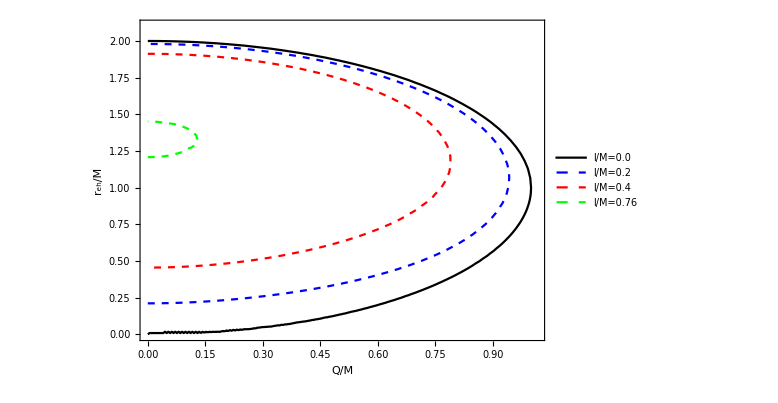

```mathematica
ContourPlot[{f[r,Q,0.0]==0,f[r,Q,0.2]==0,f[r,Q,0.4]==0,f[r,Q,0.76]==0},{Q,0,1},{r,0.0000003(*1/0 nol bolgani uchun*),2.},PlotLegends->Placed[{"l/M=0.0","l/M=0.2","l/M=0.4","l/M=0.76"},{Scaled[{0.3,0.35}],{0,0.0}}],ContourStyle->{{Black},{Dashed,Blue},{Dashed,Red},{Dashed,Green}},FrameLabel->{" Q/M","r_eh/M"},AspectRatio->0.7,Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Large,PlotRange->{ {0,1.015},{0.,2.1} }]
(*Subscript[r, eh] =NSolve[f[r,Q,l]==0,r,Reals]/.{{Q->0.0},{l->0.4}}*)
```

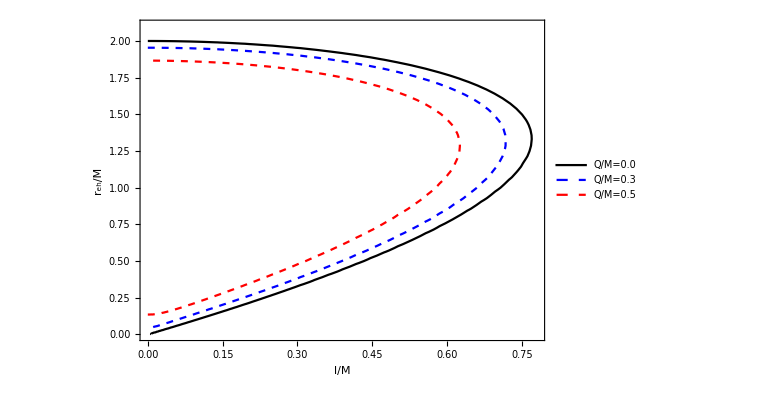

```mathematica
ContourPlot[{f[r,0.0,l]==0,f[r,0.3,l]==0,f[r,0.5,l]==0},{l,0,0.78},{r,0.0000001(*1/0 nol bolgani uchun*),2.},PlotLegends->Placed[{"Q/M=0.0","Q/M=0.3","Q/M=0.5"},{Scaled[{0.77,0.15}],{0.2,0.5}}],ContourStyle->{{Black},{Dashed,Blue},{Dashed,Red}},FrameLabel->{" l/M","r_eh/M"},AspectRatio->0.7,Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Large,PlotRange->{ {0,0.78},{0.,2.1} }]
```

## Radial dependence of the redshift of photons emitted from the geodesic particles on the equatorial plane

-1+(r^2 (-Q^2+2 r))/(r^4+l^2 (Q^2+2 r))

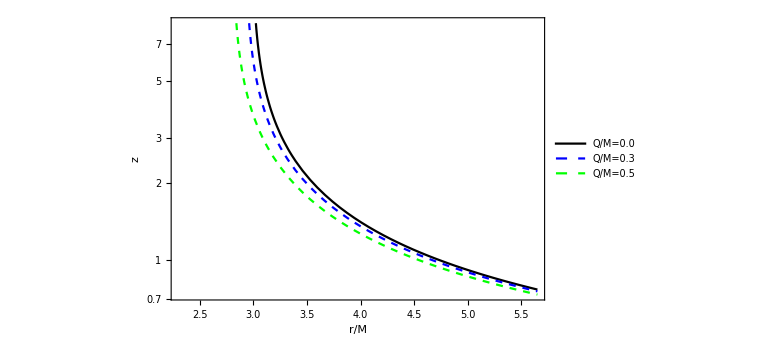

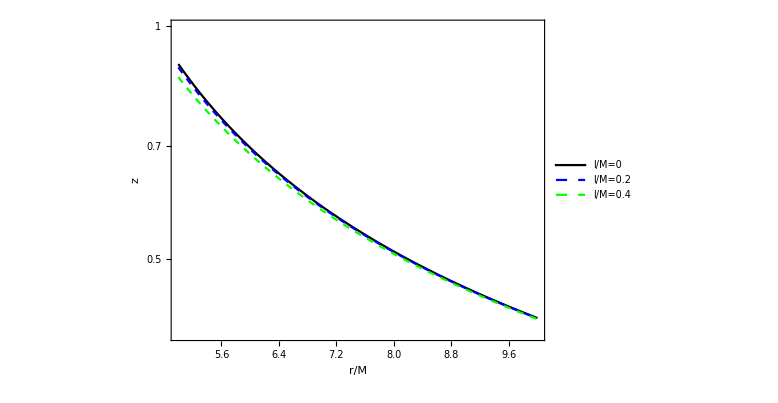

```mathematica
(*relative variation of frequency so z[r,l,Q] *)
g00[r_]=-(1-((2 * r - Q^2)*r^2)/(r^4 + (2 * r + Q^2)*l^2))
z[r_,l_,Q_]= √((-r^2* D[g00[r],r])/(g00[r]*(2*r *g00[r]-r^2* D[g00[r],r])));//Simplify
LogPlot[{z[r,0.2,0],z[r,0.2,0.3],z[r,0.2,0.5]},{r,2.3,5.65},PlotStyle->{{Black},{Dashed,Blue},{Dashed,Green}},FrameStyle->Directive[Black,13],Frame->True,FrameLabel->{"r/M","z", "l/M=0.2"},PlotLegends->Placed[{"Q/M=0.0","Q/M=0.3","Q/M=0.5"},{Scaled[{0.65,0.78}],{0,0.5}}],Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Large,Epilog->Inset[Plot[{z[r,0,0],z[r,0.2,0.3],z[r,0.4,0.5]},{r,5.8,7},PlotStyle->{{Black},{Dashed,Blue},{Dashed,Green}},Frame->True,ImageSize->360/2.2],{5.1,0.55}]]


LogPlot[{z[r,0,0.3],z[r,0.4,0.3],z[r,0.8,0.3]},{r,5.,10},PlotRange->{0.4,1},PlotStyle->{{Black},{Dashed,Blue},{Dashed,Green}},FrameLabel->{"r/M","z","Q/M=0.3"},Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Large,PlotLegends->Placed[{"l/M=0","l/M=0.2","l/M=0.4"},{Scaled[{0.70,0.78}],{0,0.5}}],AspectRatio->0.7,Epilog->Inset[Plot[{z[r,0,0],z[r,0.2,0.3],z[r,0.4,0.5]},{r,7.5,8.5},PlotStyle->{{Black},{Dashed,Blue},{Dashed,Green}},Frame->True,ImageSize->360/2.15],{9.1,-0.55}]]
```

## Density Plots for z

```mathematica
Exit
r=5.;

DensityPlot[√((r^2 (r^8 (-Q^2+r)-l^2 r^5 (3 Q^2+2 r)+l^4 (Q^6-8 Q^2 r^2-8 r^3)))/(l^6 (Q^2+2 r)^3+l^4 r^2 (Q^6+12 Q^2 r^3+4 r^3 (-2+3 r)+Q^4 r (4+3 r))+r^8 (2 Q^4+Q^2 r (-7+3 r)+r^2 (6-5 r+r^2))+l^2 r^5 (2 r^3 (-7+3 r)+Q^4 (2+4 r)+Q^2 r (-4+3 r+3 r^2)))),{Q,0,1.0},{l,0.0,0.8},ColorFunction->"Rainbow",PlotLegends->BarLegend[ Automatic,LegendLabel->"z",LegendMarkerSize->280],FrameLabel->{"Q/M","l/M", "r/M=5"},Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Large]
```

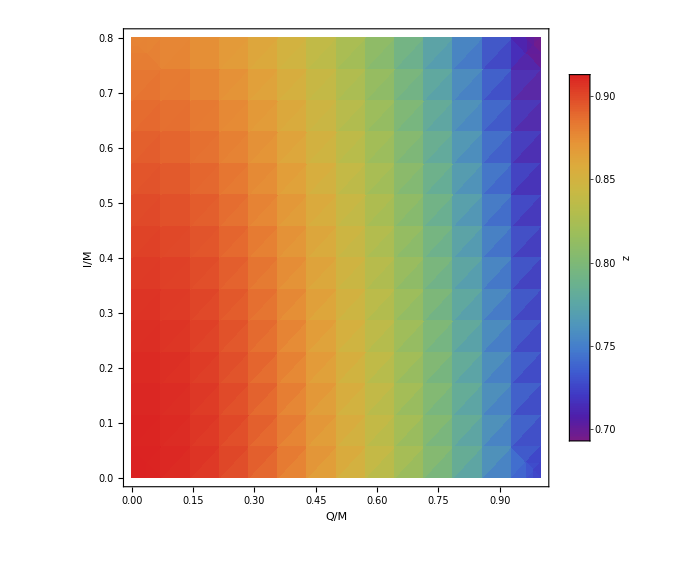

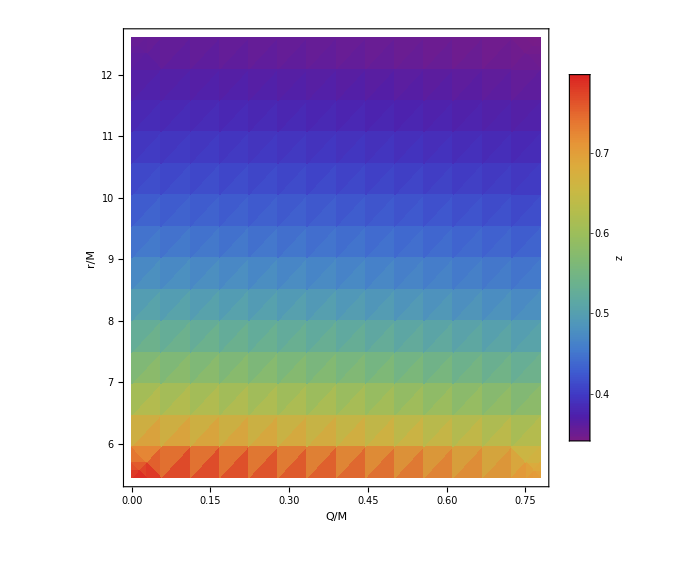

```mathematica
lz=0.4;

DensityPlot[√((r^2 (r^8 (-Q^2+r)-lz^2 r^5 (3 Q^2+2 r)+lz^4 (Q^6-8 Q^2 r^2-8 r^3)))/(lz^6 (Q^2+2 r)^3+lz^4 r^2 (Q^6+12 Q^2 r^3+4 r^3 (-2+3 r)+Q^4 r (4+3 r))+r^8 (2 Q^4+Q^2 r (-7+3 r)+r^2 (6-5 r+r^2))+lz^2 r^5 (2 r^3 (-7+3 r)+Q^4 (2+4 r)+Q^2 r (-4+3 r+3 r^2)))),{Q,0.0,0.779},{r,5.45,12.6},ColorFunction->"Rainbow",PlotLegends->BarLegend[ Automatic,LegendLabel->"z",LegendMarkerSize->280],FrameLabel->{"Q/M","r/M","l/M=0.4"},Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Large]
```

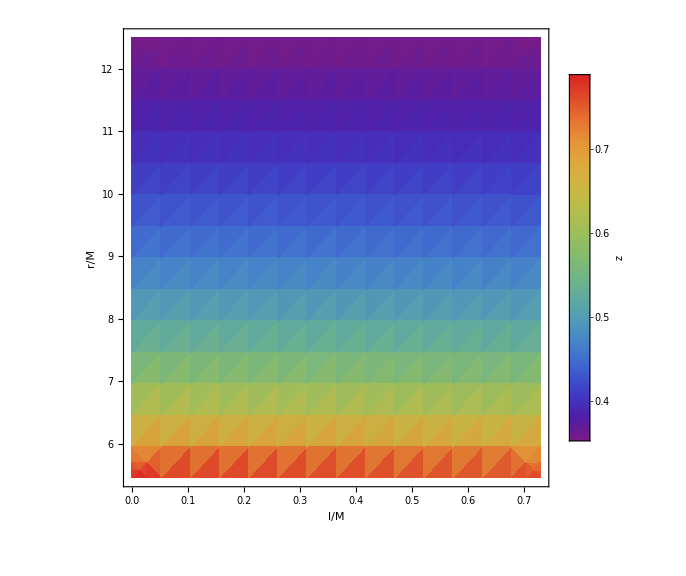

{{r→0.},{r→0.},{r→1.61257},{r→3.72076}}

```mathematica
Qz=0.3;

DensityPlot[√((r^2 (r^8 (-Qz^2+r)-l^2 r^5 (3 Qz^2+2 r)+l^4 (Qz^6-8 Qz^2 r^2-8 r^3)))/(l^6 (Qz^2+2 r)^3+l^4 r^2 (Qz^6+12 Qz^2 r^3+4 r^3 (-2+3 r)+Qz^4 r (4+3 r))+r^8 (2 Qz^4+Qz^2 r (-7+3 r)+r^2 (6-5 r+r^2))+l^2 r^5 (2 r^3 (-7+3 r)+Qz^4 (2+4 r)+Qz^2 r (-4+3 r+3 r^2)))),{l,0.0,0.73},{r,5.450,12.5},ColorFunction->"Rainbow",PlotLegends->BarLegend[ Automatic,LegendLabel->"z",LegendMarkerSize->280],FrameLabel->{"l/M","r/M","Q/M=0.3"},Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Large]
```

## Kretschman scalar nature for Hayward Charged Bh and plot

(48 M^2)/r^6

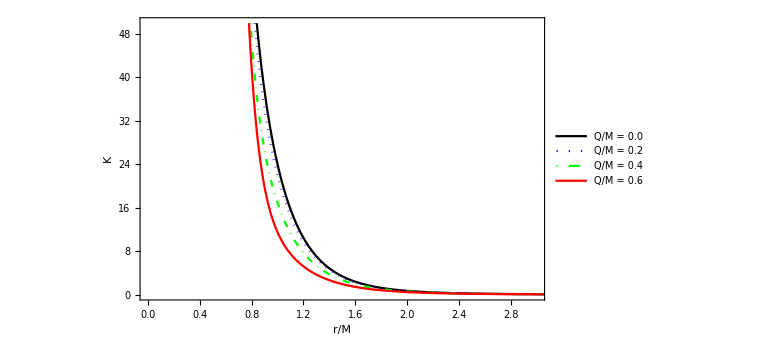

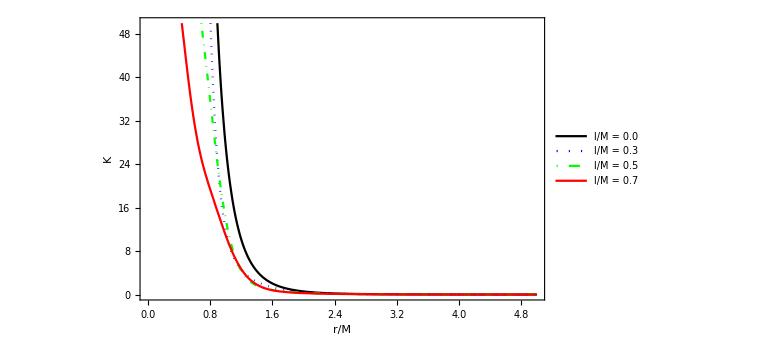

```mathematica
k[Q_,l_,M_,r_] := 1/((l^2 (2 M r+Q^2)+r^4)^6)8 (l^8 (192 M^6 r^6+384 M^5 Q^2 r^5+240 M^4 Q^4 r^4+16 M^3 Q^6 r^3-28 M^2 Q^8 r^2-4 M Q^10 r+3 Q^12)-2 l^6 r^4 (48 M^5 r^5+120 M^4 Q^2 r^4+76 M^3 Q^4 r^3-38 M^2 Q^6 r^2-38 M Q^8 r+5 Q^10)+2 l^4 r^8 (216 M^4 r^4+180 M^3 Q^2 r^3-131 M^2 Q^4 r^2-80 M Q^6 r+37 Q^8)+2 l^2 r^12 (-24 M^3 r^3+24 M^2 Q^2 r^2+34 M Q^4 r-17 Q^6)+r^16 (6 M^2 r^2-12 M Q^2 r+7 Q^4)) ;
k[0,0,M,r]//Simplify

Plot[{k[0.0,0.2,1,r],k[0.2,0.2,1,r],k[0.4,0.2,1,r],k[0.6,0.2,1,r]}, {r,0,5},FrameLabel->{"r/M", "K","l/M=0.2"},PlotLegends->Placed[{"Q/M = 0.0 ","Q/M = 0.2","Q/M = 0.4", "Q/M = 0.6"},{Scaled[{0.65,0.78}],{0,0.5}}],Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Large,PlotStyle->{{Black},{Dotted, Blue},{DotDashed,Green},{Dashing,Red}},PlotRange->{{0.,3},{-0.0,50}}]
Plot[{k[0.5,0.,1,r],k[0.5,0.3,1,r],k[0.5,0.5,1,r],k[0.3,0.7,1,r]}, {r,0.2,5},FrameLabel->{"r/M", "K","Q/M=0.3"},PlotLegends->Placed[{"l/M = 0.0 ","l/M = 0.3","l/M = 0.5", "l/M = 0.7"},{Scaled[{0.65,0.78}],{0,0.5}}],Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Large,PlotStyle->{{Black},{Dotted, Blue},{DotDashed,Green},{Dashing,Red}},PlotRange->{{0.,5},{-0.0,50}}]
```

```mathematica
DensityPlot[k[Q,.2,1,r],{Q,0.87,1.},{r,2,3},ColorFunction->"Rainbow",PlotLegends->BarLegend[ Automatic,LegendLabel->"K",LegendMarkerSize->280],FrameLabel->{"Q/M","r/M","l/M=0.2"},Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Large,PlotRange->All]
```

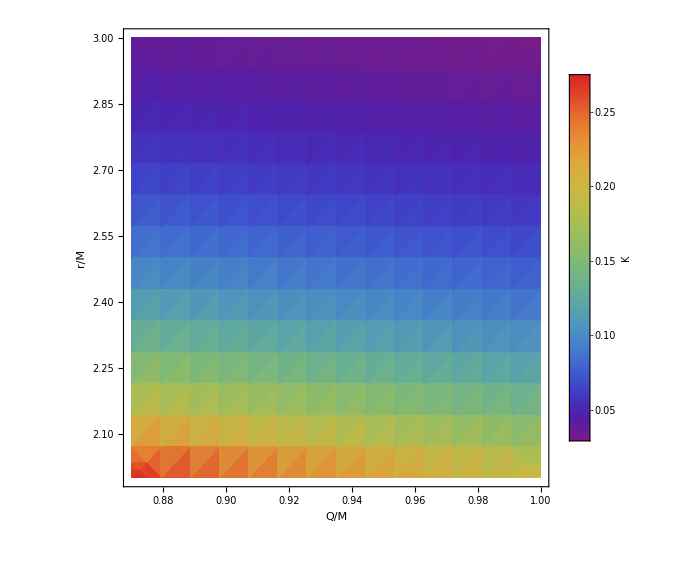

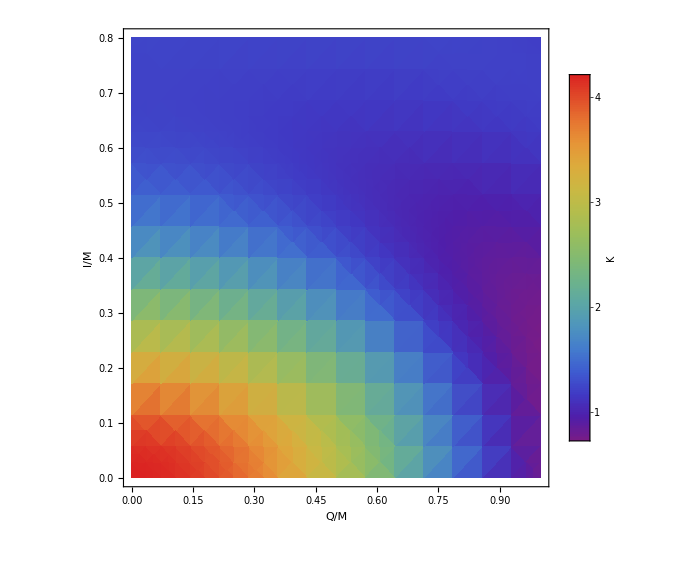

```mathematica
DensityPlot[k[Q,l,1,1.5],{Q,0.,1},{l,.0,0.8},ColorFunction->"Rainbow",PlotLegends->BarLegend[ Automatic,LegendLabel->"K",LegendMarkerSize->280],FrameLabel->{"Q/M","l/M","r/M=1.5"},Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Large,PlotRange->{{0.,1},{0.,0.8}}]
```